```mathematica
Quit
```

```mathematica
(* Theory *)
```

```mathematica
(* Parameters and options *)
```

```mathematica
SetDirectory[NotebookDirectory[]];
om0=0.3;
w0=-1;
σ80=0.8;
ga0=-0.627;
σa0=-3.562;
m10=2;
m20=2;
aini=10^-3;
zmax=2.5;
```

```mathematica
(* end *)
```

```mathematica
(* Definitions for vanilla wCDM *)
```

```mathematica
dLwCDM[a_,om_,w_]:=2/(a √om)(Hypergeometric2F1[1/2,-1/(6w),1-1/(6w),1-1/om]-√a Hypergeometric2F1[1/2,-1/(6w),1-1/(6w),(1-1/om)a^(-3w)]);
HwCDM[a_,w_,om_]:=√(om a^-3+(1-om)a^(-3(1+w)));
δwCDM[a_,w_,Ω_]:=a Hypergeometric2F1[1/(-3w),1/2-1/(2 w),1-5/(6 w),a^(-3 w) (1-1/Ω)]
fwCDM[a_,w_,Ω_]:=aa D[Log[δwCDM[aa,w,Ω]],aa]/.aa->a
fσ8wCDM[a_,w_,Ω_,σ8_]:=fwCDM[a,w,Ω]σ8  δwCDM[a,w,Ω]/δwCDM[1,w,Ω]
ΣwCDM[a_,w_,Ω_]:=2
ηwCDM[a_,w_,Ω_]:=1
GeffwCDM[a_,w_,Ω_]:=1
EgwCDM[a_,w_,Ω_]:=(Ω ΣwCDM[a,w,Ω])/(2fwCDM[a,w,Ω])
P2wCDM[a_,w_,Ω_]:=2 EgwCDM[a,w,Ω]
P3wCDM[a_,w_,Ω_,σ8_]:=a D[Log[fσ8wCDM[aa,w,Ω,σ8]],aa]/.aa->a
```

```mathematica
(* end *)
```

```mathematica
(* Definitions for μCDM models *)
```

```mathematica
H[a_]:=HwCDM[a,w0,om0]
Geff[a_,ga_,m1_]:=1+ga (1-a)^m1-ga (1-a)^(2m1)
Σ[a_,σa_,m2_]:=2+σa (1-a)^m2-σa (1-a)^(2m2)
solμCDM=NDSolve[{d''[a]+(3/a+H'[a]/H[a])d'[a]-3/2(om0 Geff[a,ga0,m10])/(a^5 H[a]^2)d[a]==0,d[aini]==aini,d'[aini]==1,f[a]==a d'[a]/d[a],f[aini]==1},{d,f},{a,aini,1}]//Quiet;
fσ8[a_]:=(f[aa] σ80 d[aa]/.solμCDM[[1]]/.aa->a)/(d[aa]/.solμCDM[[1]]/.aa->1)
Eg[a_]:=(Σ[a,σa0,m20] om0)/(2f[a])/.solμCDM[[1]]
P2[a_]:=2 Eg[a]
P3[a_]:=aa D[Log[f[aa] σ80 d[aa]],aa]/.solμCDM[[1]]/.aa->a
η[a_]:=-1+Σ[a,σa0,m20]/Geff[a,ga0,m10]
ηODE[a_]:=-1+(3 2Eg[aa] aa^-3)/(2 H[aa]^2(P3+2+aa D[H[aa],aa]/H[aa] ))/.P3->aa D[Log[fσ8[aa]],aa]/.aa->a
```

```mathematica
(* end *)
```

```mathematica
(* Plots *)
```

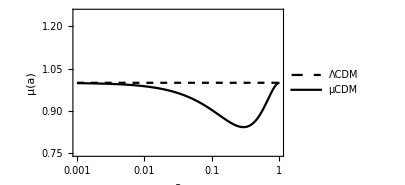
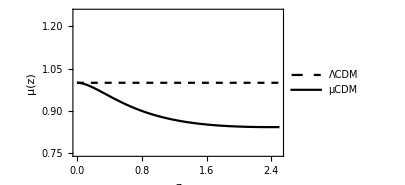

```mathematica
{LogLinearPlot[{GeffwCDM[a,w0,om0],Geff[a,ga0,m10]},{a,aini,1},Frame->True,FrameLabel->{"a","μ(a)"},FrameStyle->Black,BaseStyle->FontSize->11,PlotRange->{0.75,1.25},PlotLegends->Placed[{"ΛCDM","μCDM"},Scaled[{0.8,0.8}]],ImageSize->300,PlotStyle->{{Dashed,Black},Black}],Plot[{GeffwCDM[a,w0,om0],Geff[a,ga0,m10]}/.a->1/(1+z)//Evaluate,{z,0,zmax},Frame->True,FrameLabel->{"z","μ(z)"},FrameStyle->Black,BaseStyle->FontSize->11,PlotRange->{0.75,1.25},PlotLegends->Placed[{"ΛCDM","μCDM"},Scaled[{0.8,0.8}]],ImageSize->300,PlotStyle->{{Dashed,Black},Black}]}
```

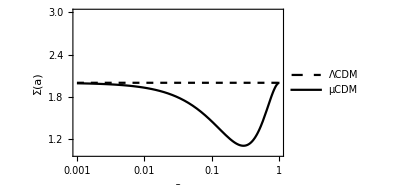
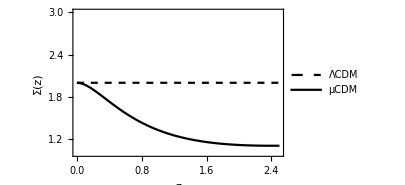

```mathematica
{LogLinearPlot[{ΣwCDM[a,w0,om0],Σ[a,σa0,m20]},{a,aini,1},Frame->True,FrameLabel->{"a","Σ(a)"},FrameStyle->Black,BaseStyle->FontSize->11,PlotRange->{1,3},PlotLegends->Placed[{"ΛCDM","μCDM"},Scaled[{0.8,0.8}]],ImageSize->300,PlotStyle->{{Dashed,Black},Black}],Plot[{ΣwCDM[a,w0,om0],Σ[a,σa0,m20]}/.a->1/(1+z)//Evaluate,{z,0,zmax},Frame->True,FrameLabel->{"z","Σ(z)"},FrameStyle->Black,BaseStyle->FontSize->11,PlotRange->{1,3},BaseStyle->FontSize->11,PlotRange->All,PlotLegends->Placed[{"ΛCDM","μCDM"},Scaled[{0.8,0.8}]],ImageSize->300,PlotStyle->{{Dashed,Black},Black}]}
```

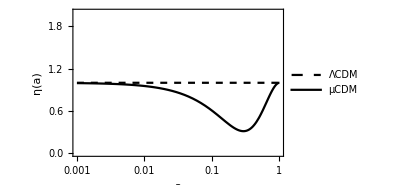
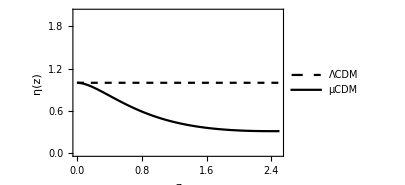

```mathematica
{LogLinearPlot[{ηwCDM[a,w0,om0],η[a]},{a,aini,1},Frame->True,FrameLabel->{"a","η(a)"},FrameStyle->Black,BaseStyle->FontSize->11,PlotRange->{0,2},PlotLegends->Placed[{"ΛCDM","μCDM"},Scaled[{0.8,0.8}]],ImageSize->300,PlotStyle->{{Dashed,Black},Black}],Plot[{ηwCDM[a,w0,om0],η[a]}/.a->1/(1+z)//Evaluate,{z,0,zmax},Frame->True,FrameLabel->{"z","η(z)"},FrameStyle->Black,BaseStyle->FontSize->11,PlotRange->{0,2},PlotLegends->Placed[{"ΛCDM","μCDM"},Scaled[{0.8,0.8}]],ImageSize->300,PlotStyle->{{Dashed,Black},Black}]}
```

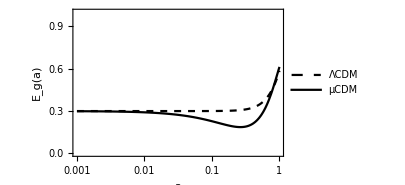
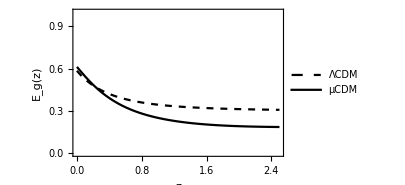

```mathematica
{LogLinearPlot[{EgwCDM[a,w0,om0],Eg[a]},{a,aini,1},Frame->True,FrameLabel->{"a","E_g(a)"},FrameStyle->Black,BaseStyle->FontSize->11,PlotRange->{0,1},PlotLegends->Placed[{"ΛCDM","μCDM"},Scaled[{0.20,0.8}]],ImageSize->300,PlotStyle->{{Dashed,Black},Black}],Plot[{EgwCDM[a,w0,om0],Eg[a]}/.a->1/(1+z)//Evaluate,{z,0,zmax},Frame->True,FrameLabel->{"z","E_g(z)"},FrameStyle->Black,BaseStyle->FontSize->11,PlotRange->{0,1},PlotLegends->Placed[{"ΛCDM","μCDM"},Scaled[{0.8,0.8}]],ImageSize->300,PlotStyle->{{Dashed,Black},Black}]}
```

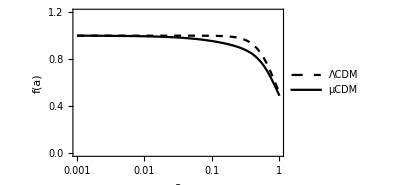
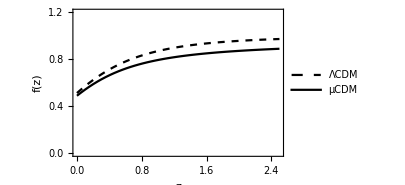

```mathematica
{LogLinearPlot[{fwCDM[a,w0,om0],f[a]/.solμCDM[[1]]},{a,aini,1},Frame->True,FrameLabel->{"a","f(a)"},FrameStyle->Black,BaseStyle->FontSize->11,PlotRange->{0,1.2},PlotLegends->Placed[{"ΛCDM","μCDM"},Scaled[{0.20,0.20}]],ImageSize->300,PlotStyle->{{Dashed,Black},Black}],Plot[{fwCDM[a,w0,om0],f[a]/.solμCDM[[1]]}/.a->1/(1+z)//Evaluate,{z,0,zmax},Frame->True,FrameLabel->{"z","f(z)"},FrameStyle->Black,BaseStyle->FontSize->11,PlotRange->{0,1.2},PlotLegends->Placed[{"ΛCDM","μCDM"},Scaled[{0.8,0.20}]],ImageSize->300,PlotStyle->{{Dashed,Black},Black}]}
```

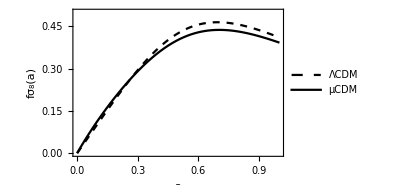
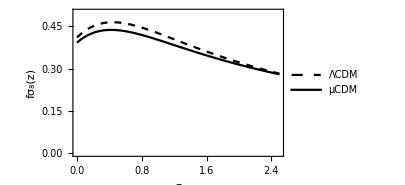

```mathematica
{Plot[{fσ8wCDM[a,w0,om0,σ80],fσ8[a]},{a,aini,1},Frame->True,FrameLabel->{"a","fσ_8(a)"},FrameStyle->Black,BaseStyle->FontSize->11,PlotRange->{0,0.5},PlotLegends->Placed[{"ΛCDM","μCDM"},Scaled[{0.8,0.20}]],ImageSize->300,PlotStyle->{{Dashed,Black},Black}],Plot[{fσ8wCDM[a,w0,om0,σ80],fσ8[a]}/.a->1/(1+z)//Evaluate,{z,0,zmax},Frame->True,FrameLabel->{"z","fσ_8(z)"},FrameStyle->Black,BaseStyle->FontSize->11,PlotRange->{0,0.5},PlotLegends->Placed[{"ΛCDM","μCDM"},Scaled[{0.20,0.20}]],ImageSize->300,PlotStyle->{{Dashed,Black},Black}]}
```

```mathematica
(* end *)
```

```mathematica
(* Some theory *)
```

```mathematica
sol=Solve[{-k^2/a^2(Φ+Ψ)==4Pi GN Σ ρm δm,-k^2/a^2 Ψ==4Pi GN μ ρm δm,η==Φ/Ψ},{Φ,Ψ,Σ}][[1]]//FullSimplify
```

{Φ→-(4 a^2 GN π δm η μ ρm)/k^2,Ψ→-(4 a^2 GN π δm μ ρm)/k^2,Σ→(1+η) μ}

```mathematica
Solve[(P2 f)/Ωm==(1+η) μ,μ][[1]]/.η->-1+(3 P2 a^-3)/(2 H[a]^2(P3+2+a D[H[a],a]/H[a] ))/.P3->a D[Log[fs8[a]],a]/.f->fs8[a]/(∫_0^a fs8[x]/x ⅆx)/.∫_0^a fs8[x]/x ⅆx->δ[a] σ8/δm0/.fs8[a]->(a σ8 δ'[a])/δm0/.D[fs8[a]->(a σ8 δ'[a])/δm0,a]/.δ''[a]->-((3/a+H'[a]/H[a])δ'[a]-3/2(Ωm Geff[a] δ[a])/(a^5 H[a]^2))//FullSimplify
```

{μ→1. Geff[a]}

```mathematica
η->-1+(3 P2wCDM[a,-1,om0] a^-3)/(2 HwCDM[a,-1,om0]^2(a D[Log[fσ8wCDM[a,-1,om0,σ80]],a]+2+a D[HwCDM[a,-1,om0],a]/HwCDM[a,-1,om0] ))/.a->1.
```

η→1.

```mathematica
Solve[(P2 f)/Ωm==(1+η) μ,μ][[1]]
```

{μ→(f P2)/((1+η) Ωm)}

```mathematica
μ->(P2 f)/((1+η) Ωm)->(fwCDM[a,-1,om0] P2wCDM[a,-1,om0])/((1+ηwCDM[a,-1,om0]) om0)/.a->1
```

μ→(f P2)/((1+η) Ωm)→1.

```mathematica
δm[a_]:= δm0/σ8 Integrate[fs8[x]/x,{x,0,a}]
```

```mathematica
f->a δm'[a]/δm[a]
```

f→fs8[a]/(∫_0^a fs8[x]/x ⅆx)

```mathematica
(* end *)
```

```mathematica
(* end *)
```

```mathematica
(* ΛCDM mock reconstruction *)
```

```mathematica
ϵ0={-1,0,1};
(* Eg GA fit *)
EgGA[a_]:=0.299411+1/3 X (1.255226749875777-(0.11738573827400875 X^2)/(1+0.5110169398354962 X)^2-(22.65470505857993 X^2)/(1+7.001933075295533 X)^2)/.X->a^3;
(*
EgGA[a_]:=EgwCDM[a,-1,0.3]
*)
dEg[z_,a1_,a2_,a3_,a4_]:=a1+a2 z+a3 z^2+a4 z^4
fminerrEg1={22.209826238680737,{a1->0.0010290538271974718}};
fminerrEg2={22.01719454225367,{a1->0.0016539802916923517,a2->-0.0005437207430013044}};
fminerrEg3={21.925526887765216,{a1->0.0010426237546774606,a2->0.001007988695228878,a3->-0.0007236540303203385}};
fminerrEg4={21.56646375313378,{a1->0.0022976445153895624,a2->-0.004679256090271691,a3->0.004227275867261415,a4->-0.0006717651261058098}};
(* H(z) GA fit *)
H0GA=69.65194980743638;
HGA[a_]:=H0GA Sqrt[1+x (-0.9013344555444585-0.5753244381634155 x+0.02040826183394463 x^2-0.00006751090930245668 x^7)^2]/.x->1/a-1;(*HGA[a_]:=70HwCDM[a,-1,0.3]*)
dH[z_,a1_,a2_,a3_,a4_]:=a1+a2 z+a3 z^2+a4 z^4
fminerrHtot2={14.970254309718927,{a1->0.01403911346869123,a2->0.010064083410493687}};
fminerrHtot3={14.71979819010853,{a1->0.017179930530875916,a2->-0.00047902218459646367,a3->0.0064171931619953415}};
fminerrHtot4={14.719688273261944,{a1->0.017232848040919704,a2->-0.0008543018426995123,a3->0.0068255194078517736,a4->-0.00007142751326560637}};
(* fσ8 GA fit *)
off=1.0190479959998808;
fσ8GA0[x_]:=-3/2 x (1+(0.00007074049783457046 x^2)/(1+0.025146535651511925 x)^2+(0.0011052461187478896 x^4)/(1-0.2667416857485918 x)^4-(13.134124478340931 x^2)/(1+3.7209313592563973 x)^2-(3.5894692130968044 x^4)/(1+5.046759958094881 x)^4);
fσ8GAa[a_]:=fσ8GA0[x]/.x->a^3;
fσ8GA[a_]:=a(off+fσ8GAa[a])
(*fσ8GA[a_]:=fσ8wCDM[a,-1,0.3,0.8]*)
fminerrfs81={22.766863024390712,{a1->0.0011506195227987822}};
fminerrfs82={22.712060099547855,{a1->0.0014839075478897373,a2->-0.00029992324393116987}};
fminerrfs83={22.45398360018358,{a1->0.0005662488215738217,a2->0.0023301585159396935,a3->-0.001263171220012977}};
fminerrfs84={21.740764991826175,{a1->0.002064863468707739,a2->-0.005669086923890014,a3->0.006098737660415577,a4->-0.0010374551035777259}};
dfs8[z_,a1_,a2_,a3_,a4_]:=a1+a2 z+a3 z^2+a4 z^4
(* Others *)
fGA[a_?NumericQ]:=fσ8GA[a]/NIntegrate[fσ8GA[x]/x,{x,0,a}]
P3GA[a_]:=a D[Log[fσ8GA[a]],a];
ηGA[a_]:=-1+(3 EgGA[a] a^-3)/((HGA[a]/H0GA)^2(P3GA[a]+2+a D[HGA[a],a]/HGA[a] ))
Ωm=1/NIntegrate[3 fσ8GA[a]/fσ8GA[1] NIntegrate[fσ8GA[y]/(y fσ8GA[1]),{y,0,a}],{a,0,1}]//Quiet
σ8GA0=NIntegrate[fσ8GA[xx]/xx,{xx,0,1}]
μGA[a_]:=(2fGA[a] EgGA[a])/((1+ηGA[a]) om)
```

0.290216

0.795708

```mathematica
(*
η->-1+(3 Eg a^-3)/(H[a]^2(P3+2+a D[H[a],a]/H[a] ))
*)
```

```mathematica
(* Ωm from growth and Eg *)
{Ωm,EgGA[0]}
```

{0.290216,0.299411}

```mathematica
(* error terms *)
```

```mathematica
δP3GA[a_?NumericQ]:=-aa(dfs8[1/aa-1,a1,a2,0,0] D[fσ8GA[aa],aa])/fσ8GA[aa]^2+aa D[dfs8[1/aa-1,a1,a2,0,0],aa]/fσ8GA[aa]/.fminerrfs82[[2]]/.aa->a
```

```mathematica
δfGA[a_?NumericQ]:=fGA[a]/fσ8GA[a](dfs8[1/a-1,a1,a2,0,0]-fGA[a]NIntegrate[dfs8[1/aa-1,a1,a2,0,0]/aa/.fminerrfs82[[2]],{aa,0.1,a}])/.fminerrfs82[[2]]
```

```mathematica
δHGA[a_]:=dH[1/a-1,a1,a2,0,0]/.fminerrHtot2[[2]];
δEgGA[a_]:=dEg[1/a-1,a1,a2,0,0]/.fminerrEg2[[2]];
```

```mathematica
δμGA[aa_]:=1/(3 om)2 a^3 (HGA[a]/H0GA ((2+P3GA[a]) δfGA[a]+fGA[a] δP3GA[a])+a fGA[a] δHGA[a] HGA'[a]/H0GA+HGA[a]/H0GA (a δfGA[a] HGA'[a]/H0GA+fGA[a] (2 (2+P3GA[a]) δHGA[a]+a δHGA'[a])))/.a->aa//Abs
```

```mathematica
δηGA[aa_]:=-((3 ((HGA[a]/H0GA)^2 (-(2+δP3GA[a]) δEgGA[a]+EgGA[a] δP3GA[a])+a EgGA[a] δHGA[a] HGA'[a]/H0GA+HGA[a]/H0GA (-a δEgGA[a] HGA'[a]/H0GA+EgGA[a] (2 (2+P3GA[a]) δHGA[a]+a δHGA'[a]))))/(a^3 (HGA[a]/H0GA)^2 (HGA[a]/H0GA (2+P3GA[a])+a HGA'[a]/H0GA)^2))/.a->aa//Abs
```

```mathematica
(* end *)
```

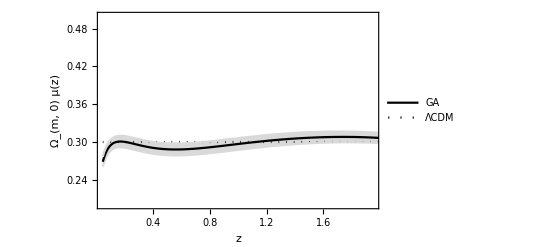

```mathematica
plμ=Plot[{om0,Ωm(μGA[aa]+ϵ0 δμGA[aa])/.om->Ωm}/.aa->1/(1+z)//Evaluate,{z,0.05,2},PlotLegends->Placed[LineLegend[{Black,{Dotted,Black}},{"GA","ΛCDM"}],Scaled[{0.82,0.78}]],Frame->True,FrameStyle->Black,PlotStyle->{{Dotted,Black},LightGray,Black,LightGray},Filling->{2->{{4},LightGray}},FrameLabel->{"z","Ω_(m, 0) μ(z)"},PlotRange->{{0.05,1.95},{0.2,0.5}},BaseStyle->FontSize->16,ImageSize->400]
```

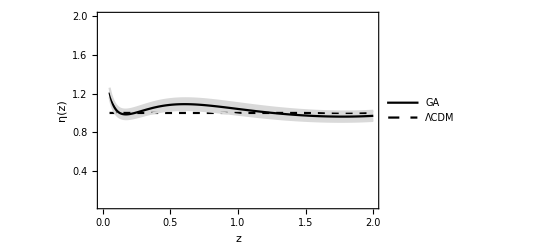

```mathematica
plη=Plot[{1,ηGA[aa]+ϵ0 δηGA[aa]}/.aa->1/(1+z)//Evaluate,{z,0.05,2},PlotLegends->Placed[LineLegend[{Black,{Dashed,Black}},{"GA","ΛCDM"}],Scaled[{0.8,0.8}]],Frame->True,FrameStyle->Black,PlotStyle->{{Dashed,Black},LightGray,Black,LightGray},FrameLabel->{"z","η(z)"},PlotRange->{{0.0,2},{0.05,2}},Filling->{2->{{4},LightGray}},ImageSize->400,BaseStyle->FontSize->16]
```

```mathematica
Export["mock_LCDM_mu.pdf",plμ,ImageSize->600]
Export["mock_LCDM_eta.pdf",plη,ImageSize->600]
```

mock_LCDM_mu.pdf

mock_LCDM_eta.pdf

```mathematica
(* end *)
```

```mathematica
(* μCDM mock reconstruction *)
```

```mathematica
ϵ0={-1,0,1};
(* Eg GA fit *)
EgGA[a_]:=0.16498003165278965+1/3 X (2.24649912884584-1.024133973936102 X+0.11796789241018021 X^4)/.X->a^3;
(*
EgGA[a_]:=EgwCDM[a,-1,0.3]
*)
dEg[z_,a1_,a2_,a3_,a4_]:=a1+a2 z+a3 z^2+a4 z^4
fminerrEg1={21.64331518007955,{a1->0.0007086806728162069}};
fminerrEg2={21.287731950670242,{a1->0.0014704947865886286,a2->-0.000584131803582251}};
fminerrEg3={21.251751898098256,{a1->0.0010955641662216504,a2->0.0002362211781140992,a3->-0.0003573898760701666}};
fminerrEg4={21.187082292180243,{a1->0.0005597704525283743,a2->0.00235226156430705,a3->-0.002065984455939467,a4->0.0002141176978846722}};
(* H(z) GA fit *)
H0GA=69.65194980743638;
HGA[a_]:=H0GA Sqrt[1+x (-0.9013344555444585-0.5753244381634155 x+0.02040826183394463 x^2-0.00006751090930245668 x^7)^2]/.x->1/a-1;(*HGA[a_]:=70HwCDM[a,-1,0.3]*)
dH[z_,a1_,a2_,a3_,a4_]:=a1+a2 z+a3 z^2+a4 z^4
fminerrHtot2={14.970254309718927,{a1->0.01403911346869123,a2->0.010064083410493687}};
fminerrHtot3={14.71979819010853,{a1->0.017179930530875916,a2->-0.00047902218459646367,a3->0.0064171931619953415}};
fminerrHtot4={14.719688273261944,{a1->0.017232848040919704,a2->-0.0008543018426995123,a3->0.0068255194078517736,a4->-0.00007142751326560637}};
(* fσ8 GA fit *)
off=1.1547007473302673;
fσ8GA0[X_]:=-0.8652275944329362 X^0.42723143508048267+0.10656616386919483 X^1.877727974263708-0.014974203366821854 X^8.109630440536886;
fσ8GAa[a_]:=fσ8GA0[x]/.x->a^3;
fσ8GA[a_]:=a(off+fσ8GAa[a])
(*fσ8GA[a_]:=fσ8wCDM[a,-1,0.3,0.8]*)
fminerrfs81={23.70791866280233,{a1->0.0010590727283306418}};
fminerrfs82={23.521961116216623,{a1->0.0016426582956896635,a2->-0.0005349725920024151}};
fminerrfs83={22.805627942408854,{a1->0.0001783504090957819,a2->0.0036709141401678005,a3->-0.002034735772770342}};
fminerrfs84={21.5798455596902,{a1->0.002056302945100829,a2->-0.006321227362188755,a3->0.007202964091289675,a4->-0.0013145920913417996}};
dfs8[z_,a1_,a2_,a3_,a4_]:=a1+a2 z+a3 z^2+a4 z^4
(* Others *)
fGA[a_?NumericQ]:=fσ8GA[a]/NIntegrate[fσ8GA[x]/x,{x,0,a}]
P3GA[a_]:=a D[Log[fσ8GA[a]],a];
ηGA[a_]:=-1+(3 EgGA[a] a^-3)/((HGA[a]/H0GA)^2(P3GA[a]+2+a D[HGA[a],a]/HGA[a] ))
Ωm=1/NIntegrate[3 fσ8GA[a]/fσ8GA[1] NIntegrate[fσ8GA[y]/(y fσ8GA[1]),{y,0,a}],{a,0,1}]//Quiet
σ8GA0=NIntegrate[fσ8GA[xx]/xx,{xx,0,1}]
μGA[a_]:=(2fGA[a] EgGA[a])/((1+ηGA[a]) om)
```

0.271304

0.790971

```mathematica
(*
η->-1+(3 Eg a^-3)/(H[a]^2(P3+2+a D[H[a],a]/H[a] ))
*)
```

```mathematica
(* Ωm from growth and Eg *)
{Ωm,EgGA[0]}
```

{0.271304,0.16498}

```mathematica
δP3GA[a_?NumericQ]:=-aa(dfs8[1/aa-1,a1,a2,0,0] D[fσ8GA[aa],aa])/fσ8GA[aa]^2+aa D[dfs8[1/aa-1,a1,a2,0,0],aa]/fσ8GA[aa]/.fminerrfs82[[2]]/.aa->a
δfGA[a_?NumericQ]:=fGA[a]/fσ8GA[a](dfs8[1/a-1,a1,a2,0,0]-fGA[a]NIntegrate[dfs8[1/aa-1,a1,a2,0,0]/aa/.fminerrfs82[[2]],{aa,0.1,a}])/.fminerrfs82[[2]]
δHGA[a_]:=dH[1/a-1,a1,a2,0,0]/.fminerrHtot2[[2]];
δEgGA[a_]:=dEg[1/a-1,a1,a2,0,0]/.fminerrEg2[[2]];
δμGA[aa_]:=1/(3 om)2 a^3 (HGA[a]/H0GA ((2+P3GA[a]) δfGA[a]+fGA[a] δP3GA[a])+a fGA[a] δHGA[a] HGA'[a]/H0GA+HGA[a]/H0GA (a δfGA[a] HGA'[a]/H0GA+fGA[a] (2 (2+P3GA[a]) δHGA[a]+a δHGA'[a])))/.a->aa//Abs
δηGA[aa_]:=-((3 ((HGA[a]/H0GA)^2 (-(2+δP3GA[a]) δEgGA[a]+EgGA[a] δP3GA[a])+a EgGA[a] δHGA[a] HGA'[a]/H0GA+HGA[a]/H0GA (-a δEgGA[a] HGA'[a]/H0GA+EgGA[a] (2 (2+P3GA[a]) δHGA[a]+a δHGA'[a]))))/(a^3 (HGA[a]/H0GA)^2 (HGA[a]/H0GA (2+P3GA[a])+a HGA'[a]/H0GA)^2))/.a->aa//Abs
```

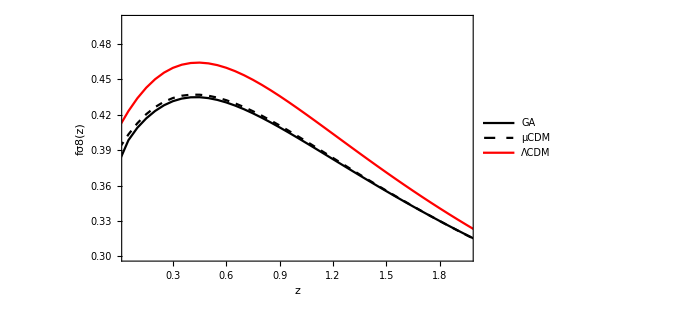

```mathematica
datafs8=Table[{z,fσ8GA[a]/.a->1/(1+z)},{z,0,2,0.05}];
datafs80=Table[{z,σ80(f[a]d[a]/.solμCDM[[1]]/.a->1/(1+z))/(d[a]/.solμCDM[[1]]/.a->1)},{z,0,2,0.05}];
datafs8w0=Table[{z,fσ8wCDM[1/(1+z),-1,om0,σ80]},{z,0,2,0.05}];
ListPlot[{datafs80,datafs8,datafs8w0},Joined->True,PlotLegends->Placed[LineLegend[{Black,{Dashed,Black},Red},{"GA","μCDM","ΛCDM"}],Scaled[{0.8,0.8}]],Frame->True,FrameStyle->Black,PlotStyle->{{Dashed,Black},Black,Red},FrameLabel->{"z","fσ8(z)"},PlotRange->{{0.05,1.95},{0.3,.5}},BaseStyle->FontSize->16,ImageSize->500]
```

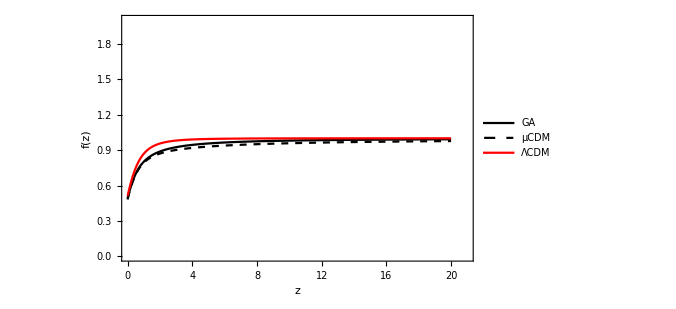

```mathematica
dataf=Table[{z,fGA[aa]/.aa->1/(1+z)},{z,0,20,0.05}];
dataf0=Table[{z,f[a]/.solμCDM[[1]]/.a->1/(1+z)},{z,0,20,0.05}];
datafw0=Table[{z,fwCDM[1/(1+z),-1,om0]},{z,0,20,0.05}];
ListPlot[{dataf0,dataf,datafw0},Joined->True,PlotLegends->Placed[LineLegend[{Black,{Dashed,Black},Red},{"GA","μCDM","ΛCDM"}],Scaled[{0.8,0.8}]],Frame->True,FrameStyle->Black,PlotStyle->{{Dashed,Black},Black,Red},FrameLabel->{"z","f(z)"},PlotRange->{{0.05,20.95},{0,2}},BaseStyle->FontSize->16,ImageSize->500]
```

```mathematica
fga=fσ8GA[a]/Integrate[fσ8GA[x]/x,{x,0,a}]//PowerExpand
```

(a (1.1547-0.865228 a^1.28169+0.106566 a^5.63318-0.0149742 a^24.3289))/(1.1547 a+a^1. (-0.379204 a^1.28169+0.0160656 a^5.63318-0.000591191 a^24.3289))

```mathematica
Solve[Σ==μ(1+η),η][[1]]//Expand
```

{η→-1+Σ/μ}

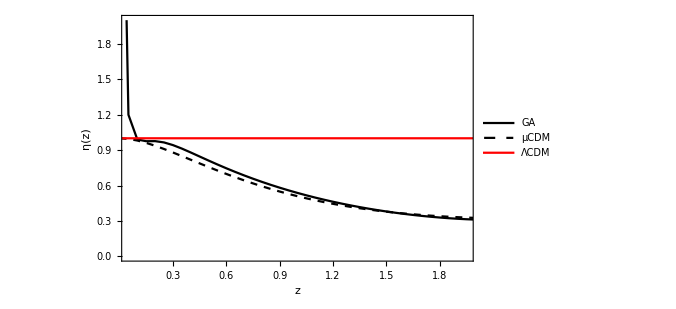

```mathematica
dataη=Table[{z,ηGA[aa]/.om->Ωm/.aa->1/(1+z)},{z,0,2,0.05}];
dataη0=Table[{z,-1+Σ[1/(1+z),σa0,m20]/Geff[1/(1+z),ga0,m10]},{z,0,2,0.05}];
dataηw=Table[{z,1},{z,0,2,0.05}];
ListPlot[{dataη0,dataη,dataηw},Joined->True,PlotLegends->Placed[LineLegend[{Black,{Dashed,Black},Red},{"GA","μCDM","ΛCDM"}],Scaled[{0.8,0.8}]],Frame->True,FrameStyle->Black,PlotStyle->{{Dashed,Black},Black,Red},FrameLabel->{"z","η(z)"},PlotRange->{{0.05,1.95},{0,2}},BaseStyle->FontSize->16,ImageSize->500]
```

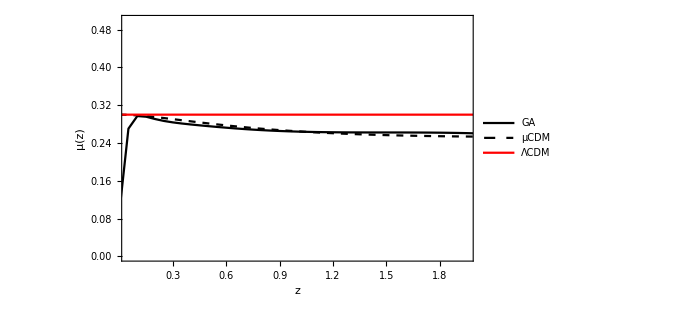

```mathematica
dataG=Table[{z,(2fGA[a]EgGA[a])/(1+ηGA[a])/.solμCDM[[1]]/.a->1/(1+z)},{z,0,2,0.05}];
dataG0=Table[{z,om0 Geff[1/(1+z),ga0,m10]},{z,0,2,0.05}];
dataGw=Table[{z,om0},{z,0,2,0.05}];
ListPlot[{dataG0,dataG,dataGw},Joined->True,PlotLegends->Placed[LineLegend[{Black,{Dashed,Black},Red},{"GA","μCDM","ΛCDM"}],Scaled[{0.8,0.8}]],Frame->True,FrameStyle->Black,PlotStyle->{{Dashed,Black},Black,Red},FrameLabel->{"z","μ(z)"},PlotRange->{{0.05,1.95},{0,0.5}},BaseStyle->FontSize->16,ImageSize->500]
```

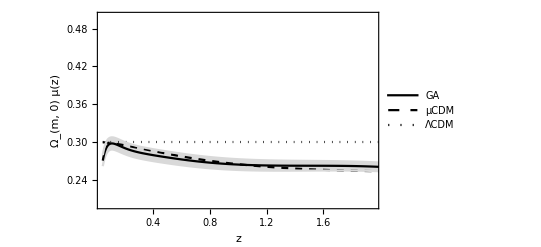

```mathematica
plμ=Plot[{om0,om0 Geff[aa,ga0,m10],Ωm(μGA[aa]+ϵ0 δμGA[aa])/.om->Ωm}/.aa->1/(1+z)//Evaluate,{z,0.05,2},PlotLegends->Placed[LineLegend[{Black,{Dashed,Black},{Dotted,Black}},{"GA","μCDM","ΛCDM"}],Scaled[{0.82,0.78}]],Frame->True,FrameStyle->Black,PlotStyle->{{Dotted,Black},{Dashed,Black},LightGray,Black,LightGray},Filling->{3->{{5},LightGray}},FrameLabel->{"z","Ω_(m, 0) μ(z)"},PlotRange->{{0.05,1.95},{0.2,0.5}},BaseStyle->FontSize->16,ImageSize->400]
```

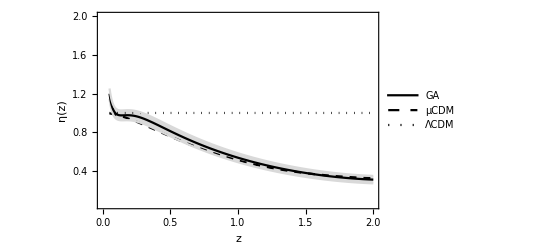

```mathematica
plη=Plot[{1,Σ[aa,σa0,m20]/Geff[aa,ga0,m10]-1,ηGA[aa]+ϵ0 δηGA[aa]}/.aa->1/(1+z)//Evaluate,{z,0.05,2},PlotLegends->Placed[LineLegend[{Black,{Dashed,Black},{Dotted,Black}},{"GA","μCDM","ΛCDM"}],Scaled[{0.82,0.78}]],Frame->True,FrameStyle->Black,PlotStyle->{{Dotted,Black},{Dashed,Black},LightGray,Black,LightGray},FrameLabel->{"z","η(z)"},PlotRange->{{0.0,2},{0.05,2}},Filling->{3->{{5},LightGray}},BaseStyle->FontSize->16,ImageSize->400]
```

```mathematica
Export["mock_muCDM_mu.pdf",plμ,ImageSize->600]
Export["mock_muCDM_eta.pdf",plη,ImageSize->600]
```

mock_muCDM_mu.pdf

mock_muCDM_eta.pdf

```mathematica
(* end *)
```